```mathematica
(*Limpia el kernel*)
ClearAll["Global`*"]
```

```mathematica
(*Representaremos TODAS las rotaciones en el sistema a traves de matrices de rotacion con argumento simbolico. Si bien esto es molesto, nos da varias ventajas, trasnformar entre coordenadas entre sistemas es trivial, y la obtencion del vector de velocidad angular es una operacion sistematica. Como desventaja, existen ambiguedades bien conocidas en el uso de matrices de rotacion, en particular, la "direccion" en que las matrices transforman, y el orden en que las matrices se multiplican para componer una rotacion general consistente de multiples rotaciones parciales

Estas matrices de transformacion son las estandares usadas en Matematicas, para expresar rotaciones de vectores COLUMNA, en Mathematica, especificamos funciones que quiza puedan tomar argumentos con la sintaxis de un guion bajo luego del argumento, y el operador dos punto igual, o de evaluacion demorada*)
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}});
Ry[θ_]:=({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}});
Rz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
(*La funcion siguiente calcula el tensor de velocidad angular (GetWx) y de este podemos obtener el vector de velocidad angular devolviendo algunos de sus componentes en ubicaciones especificas con la funcion GetW, dada cierta matriz de rotacion simbolica que describa las rotaciones que lleven de un sistema inercial O a un sistema final P, y, dependiendo de la matriz de rotacion usada, quiza obteniendo la velocidad angular de P en terminos de O, o viceversa, diremos que ω es el prefijo de las velocidades expresadas en terminos de O, en tanto Ω es el prefijo de las velocidades expresadas en terminos de P en lo sucesivo

Las velocidades angulares son importantes, porque se necesitan para determinar las energias rotacionales de los cuerpos*)
GetWx[Rmt_]:=D[Rmt,t].Transpose[Rmt];
GetW[Rmt_]:={{GetWx[Rmt][[3]][[2]]},{GetWx[Rmt][[1]][[3]]},{GetWx[Rmt][[2]][[1]]}};
```

```mathematica
(*Rotaciones al sistema de referencia de la propia esfera*)
EsfPrimRot = Rz[0];
EsfSecRot = Ry[0];
EsfTerRot = Rx[ϕsph[t]];
(*Rotaciones del cuerpo de la esfera al sistema del péndulo*)
PendSecRot = Ry[0];
PendPrimRot = Rx[βpend[t]];

(*ADD IN LIN!!!
Vamosa suponer que se aniade  un grado de libertad adicional consistente del voltaje del motor, pero lo trataremos en momentos posteriores del desarrollo del sistema, y que la velocidad del motor es igual a alguna constante de proporcionalidad por la derivada de alphapend a lo largo del tiempo, estrictamente hablando, no se trata de una rotacion, porque en forma mecanica, no hay rotaciones adicionales que puedan considerarse, pero el sistema mismo tendria algun grado de libertad dado por el modelo del robot, donde la entrada es la cantidad de voltaje...,  por lo que solo podriamos considerarlo hasta las ecuaciones de Lagrange, tratando ya no de controlar el comportamiento del angulo alphapend, si no del voltaje que se le pueda proporcionar etc etc etc, en los programas hasta el momento, aunque alphapend se considera aqui un grado de libertad, al final se proporciona el comportamiento exacto de alphapend porque se brinda como una funcion que claramente se conoce en todo momento... por lo cual no podria considerarse un grado de libertad del sistema*)
```

```mathematica
REsf=EsfPrimRot.EsfSecRot.EsfTerRot;
RPend = REsf.PendPrimRot.PendSecRot;
```

```mathematica
(*Delta de posición al CENTRO DE MASA del péndulo, las inercias del pendulo TAMBIEN deben de darse con respecto al centro de masa del pendulo, y nada mas*)
DVecPend = RPend.{{0},{0},{-radioPendulo}};
(*Debemos aplicar el mismo razonamiento para el CENTRO DE MASA de la esfera, que incluye la placa, al menos, en el caso de la restriccion en grados de libertad, que esta un poco mas arriba que el centro geometrico de la esfera*)
DVecEsf=REsf.{{0},{0},{offsetEsf}};
```

```mathematica
(*Velocidad angular de O en terminos del sys de la esfera*)
ΩEsf= -GetW[Transpose[REsf]]//Simplify;
ωEsf= GetW[REsf]//Simplify;
(*Velocidad angular de O en términos del sys del péndulo*) 
ΩPend = -GetW[Transpose[RPend]]//Simplify;
ωPend= GetW[RPend]//Simplify;
```

```mathematica
(*Tensores de inercia, en todo caso, en la esfera podemos distinguir dos casos, o bien las inercias se expresan en terminos del centro de masa de la esfera, o en terminos del centro geometrico de la esfera, como el sistema es aun simetrico, la matriz es diagonal de todos modos, pero la posible transformacion es posible con el teorema de los ejes paralelos, como la esfera se mueve solamente en terminos del eje x, porque Z no cambia nunca, e y no cambia tampoco nunca (los angulos son cero en las matrices de rotacion puestas mas arriba, de todos modos), solo necesitamos hacer el desplazamiento considerando la masa de la esfera y el valor del offset, en el caso del pendulo, solamente hace falta obtener los datos y ponernlos directamente, la necesidad de establecer el centro geometrico de la esfera existe porque aunque la inercia del centro de masa es natural, es la inercia con respecto al centro de giro la que importa, la mayor parte de los programa s de cad solo pueden brindar facilmente las inercias desde el centro de masa de los cuerpos del sistema, por lo que usaremos esa y aplicaremos el teorema de los ejes paralelos que dice que:

I=Io+m*d*d

Donde en el modelo simplificado solo es necesario hacer la correccion en la inercia sobre el eje XX

los efectos adicionales, digamos, por la masa de la esfera se pueden condierar adicionalmente para sus contribuciones NO rotacionales, y en realidad estaria bien hacer esa sola distincion
*)
InertiaPendulo =({{IxxP, 0, 0}, {0, IyyP, 0}, {0, 0, IzzP}});
InertiaSph=({{IxxS, 0, 0}, {0, IyyS, 0}, {0, 0, IzzS}});
```

```mathematica
(*Energia rotacional de la esfera*)
EROTESF=0.5*(Transpose[ΩEsf].InertiaSph.ΩEsf)[[1]][[1]];
(*Energía rotacional del péndulo*)
EROTPEND = 0.5*(Transpose[ΩPend].InertiaPendulo.ΩPend)[[1]][[1]];
```

```mathematica
(*Posición del centro GEOMETRICO de la esfera*)
VecEsfera= {{x[t]},{y[t]},{radioEsfera}};
VecEsferaMasa=VecEsfera+DVecEsf;
```

```mathematica
(*Energía cinética de la esfera, pero debe expresarse en terminos del centro de masa de la esfera*)
VelEsfera=D[VecEsferaMasa,t];
ETRASESF=(0.5*mEsf*Transpose[VelEsfera].VelEsfera)[[1]][[1]];
(*Energía cinética del péndulo, igualmente, debe expresarse en terminso del centro de masa de la esfera, pero en este caso, se parte desde el CENTRO GEOMETRICO de la esfera*)
VecPend = VecEsfera+DVecPend;
VelPend = D[VecPend,t];
ETRASPEND=(0.5*mPend*Transpose[VelPend].VelPend)[[1]][[1]];
```

```mathematica
(*Energías potenciales, una vez mas, en la esfera debe ser respecto del CENTRO DE MASA*)
gVector=Transpose[{{0},{0},{g}}];
EPOTESF   = (mEsf*gVector.VecEsferaMasa)[[1]][[1]];
EPOTPEND = (mPend*gVector.VecPend)[[1]][[1]];
```

```mathematica
(*Lagrangiano*)
T=EROTESF+EROTPEND+ETRASESF+ETRASPEND;
V=EPOTESF+EPOTPEND;
Lag=T-V //Chop;
```

```mathematica
(*Aplicación de las ecuaciones de Euler Lagrange, parte izquierda*)
EULA1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]//Chop;
EULA2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]//Chop;
EULA3=D[D[Lag,ψsph'[t]],t]-D[Lag,ψsph[t]]//Chop;
EULA4=D[D[Lag,θsph'[t]],t]-D[Lag,θsph[t]]//Chop;
EULA5=D[D[Lag,ϕsph'[t]],t]-D[Lag,ϕsph[t]]//Chop;
EULA6=D[D[Lag,αpend'[t]],t]-D[Lag,αpend[t]]//Chop;
EULA7=D[D[Lag,βpend'[t]],t]-D[Lag,βpend[t]]//Chop;
```

```mathematica
(*Restricciones*)
(*Restriccion1=(x'[t] - radioEsfera*(ωEsf[[2]][[1]]));
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));*)
(*Restricciones*)
(*Restriccion1=0;
Restriccion2=0;*)
(*En el ejemplo linealizado, NO PODEMOS USAR demasiados valores de friccion, al hacer eliminacion de variables... Pero, de todos modos queremos un modelo de relativa sencillez, aun despreciando efectos de friccion, al menos en el motor, su magnitud relativa es despreciable, y en la esfera para pequenios angulos, su magnitud relativa total es tanto dificil de estimar como necesariamente cero en el caso de una esfera perfecta, ergo, usaremos los multiplicadores de lagrange*)
(*El uso del modelo del motor NECESITA de multiplicadores de Lagrange para poder funcionar, o NDSolve se rinde rapidamente, el intneto de linealizacion se beneficia del uso de los multiplcadores de Lagragne al reducir el numero de parametros necesrios para expresar todo el sistema *)
Restriccion1=0;
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));
```

```mathematica
a11=D[Restriccion1,x'[t]];
a12=D[Restriccion1,y'[t]];
a13=D[Restriccion1,ψsph'[t]];
a14=D[Restriccion1,θsph'[t]];
a15=D[Restriccion1,ϕsph'[t]];
a16=D[Restriccion1,αpend'[t]];
a17=D[Restriccion1,βpend'[t]];

a21=D[Restriccion2,x'[t]];
a22=D[Restriccion2,y'[t]];
a23=D[Restriccion2,ψsph'[t]];
a24=D[Restriccion2,θsph'[t]];
a25=D[Restriccion2,ϕsph'[t]];
a26=D[Restriccion2,αpend'[t]];
a27=D[Restriccion2,βpend'[t]];
```

```mathematica
(*Restricciones*)
(*Restriccion1=(x'[t] - radioEsfera*(ωEsf[[2]][[1]]));
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));*)
(*fx=-fEsfX(Restriccion1);
fy=-fEsfY(Restriccion2);
fθ=-radioEsfera Cos[ψsph[t]] *fx-radioEsfera Sin[ψsph[t]] *fy;
fϕ=-radioEsfera Cos[θsph[t]] Sin[ψsph[t]] *fx+radioEsfera Cos[θsph[t]] Cos[ψsph[t]] *fy;*)
(*Restriccion1=0;
Restriccion2=0;*)
(*y haciendo las fricciones todas nulas por supuesto, porque se usaram multiplicadores de lagrange*)
fx=0;
fy=0;
fθ=0;
fϕ=0;
```

```mathematica
(*Fuerzas generalizadas*)
(*F1=λ1[t]*a11 +λ2[t]*a21 -fEsfXAir*x'[t]+fx;
F2=λ1[t]*a12 +λ2[t]*a22 -fEsfYAir*y'[t]+fy;
F3=λ1[t]*a13 +λ2[t]*a23-fEsfZ*ωEsf[[3]][[1]] ;
F4=λ1[t]*a14 +λ2[t]*a24 +fθ;
F5=λ1[t]*a15 +λ2[t]*a25 +fϕ;
F6=λ1[t]*a16 +λ2[t]*a26 +TorquePenduloAlfa[t]-fPendA*αpend'[t];
F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-fPendB*βpend'[t];*)
(*y haciendo TODAS las fricciones iguales a cero, en este caso, no hay rotamiento en z, ok, simplificar las fricciones del pendulo, ok, solo la friccion en y, pero es comparable a la del aire, y casi desprecialbe etc etc*)

TorquePenduloBeta[t]=k1mot(Volt[t]-k2mot*βpend'[t]);

(*F1=λ1[t]*a11 +λ2[t]*a21 -0*x'[t]+fx;
F2=λ1[t]*a12 +λ2[t]*a22 -fEsfYAir*y'[t]+fy
F3=λ1[t]*a13 +λ2[t]*a23-0*ωEsf[[3]][[1]] ;
F4=λ1[t]*a14 +λ2[t]*a24 +fθ;
F5=λ1[t]*a15 +λ2[t]*a25 +fϕ
F6=λ1[t]*a16 +λ2[t]*a26 +TorquePenduloAlfa[t]-0*αpend'[t];
F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-fPendB*βpend'[t]*)

(*pero conservamos las fricciones del sistema que eran tradicionales anteriormente*)

F1=λ1[t]*a11 +λ2[t]*a21 -0*x'[t]+fx;
F2=λ1[t]*a12 +λ2[t]*a22 -fEsfYAir*y'[t]+fy;
F3=λ1[t]*a13 +λ2[t]*a23-0*ωEsf[[3]][[1]];
F4=λ1[t]*a14 +λ2[t]*a24 +fθ;
F5=λ1[t]*a15 +λ2[t]*a25 +fϕ;
F6=λ1[t]*a16 +λ2[t]*a26 +TorquePenduloAlfa[t]-0*αpend'[t];
F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-0*fPendB*βpend'[t];
```

```mathematica
(*como determinar las kis del sistema, si se conocen el otrque de motor parado y el tiempo de asentamiento, ok, pues podemos asumir que el motor tiene una funcion que relaciona

t = k1(V-k2ω)

Donde k1 puede hallarse del torque del motor parado a un voltaje determinado, digamos, 12V, en el caso del pg71 con motor 9015, el torque a rotor parado es de 30 Nm a un voltaje de 12V, por lo cual

30 = k1(12-0)-> k1=30/12

Ademas de eso, del motor podemos saber ya que la velocidad a carga libre es de 216 RPM, o bien 216*2Pi rad/s, por lo cual

0 = k1(12-k2*216*2*Pi)
k2 = 12 / (216*2*Pi)
*)

(*solo para hacer tests..., tambien, son dos motores actuando en union, con velocidades individuales opeusta, pero expresadas por ejemplo como

w=(wm1+wm2)/2

el sobre dos es importante, pese a que son dos motores, casa uno NO tiene forma de reduccion en las poleas, y sus contribuciones se parten a la mitad para dar la total, podemos asumir que se trate de un unico motor de las caracterisitcas de la hoja de datos

el tiempo de asentamiento es un parametro mas o menos inutil por si mismo, existe, si, y podria agregarse un cuerpo adicional con la inercia y masa que se puedan encontrar del motor, pero no se, seria demasiado y podriamos asumir que la mayor contribucion proviene de la friccion en lugar de la masa, que se incluye ya en la del pendulo, y la inercia, que las pruebas la daban como relativamente despreciables aun para valores de salida del motor cerca del minimo posible para su movimiento
*)

(*rtest={
k1mot ->30/12,
k2mot ->12 / (216*2*Pi/60),
kprod-> (30/12)(12 / (216*2*Pi/60))}//N;

F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-fPendB*βpend'[t]/.rtest//Expand;*)
```

```mathematica
(*Composición de ecuaciones de EULA*)
eq1=EULA1-F1;
eq2=EULA2-F2;
eq3=EULA3-F3;
eq4=EULA4-F4;
eq5=EULA5-F5;
eq6=EULA6-F6;
eq7=EULA7-F7;
(*Condición de no deslizamiento*)
eqR1=Restriccion1;
eqR2=Restriccion2;
(*Condiciones de velocidad forzada*)
eqf1=αpend'[t];
eqf2=Volt[t]-1(ϕsph[t])-2(ϕsph'[t])+1(βpend[t]);
u=-((5 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]) ϕsph[t])/(2 (1/4 (9+(10 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]))/(0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])]))-(5 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]))/(2 (0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])]))) (0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])])))-((9+(10 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]))/(0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])])) (0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph[t])/(10 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]))-(2 (0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph'[t] (3+(-0.026093055573967-0.13890332234250014 Sin[βpend[t]+ϕsph[t]] βpend'[t]+0.03236710202684647 Sin[ϕsph[t]] ϕsph'[t]-0.13890332234250014 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])/(0.4278062687504448+0.032367102026846464 Cos[ϕsph[t]]-0.013726746118715057 Cos[2 (βpend[t]+ϕsph[t])])))/(5 (-0.419163868+0.16569095399999997 Cos[βpend[t]+ϕsph[t]]))
eqf2=Volt[t] -u+1(βpend[t])
```

-((5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]) ϕsph[t])/(2 (1/4 (9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))-(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])))-((9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph[t])/(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))-(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph'[t] (3+(-0.0260931-0.138903 Sin[βpend[t]+ϕsph[t]] βpend'[t]+0.0323671 Sin[ϕsph[t]] ϕsph'[t]-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])))/(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))

Volt[t]+βpend[t]+(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]) ϕsph[t])/(2 (1/4 (9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))-(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))+((9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph[t])/(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))+(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph'[t] (3+(-0.0260931-0.138903 Sin[βpend[t]+ϕsph[t]] βpend'[t]+0.0323671 Sin[ϕsph[t]] ϕsph'[t]-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])))/(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))

```mathematica
(*Eliminación de coeficiente de Lagrange de la restricción*)
(*eqs = {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,eqR1==0,eqR2==0,eqf1==0,eqf2==0};
eqsInit={eqs,
x[0]==0,x'[0]==0,
y[0]==0,y'[0]==0,
ψsph[0]==0,ψsph'[0]==0,
θsph[0]==0,θsph'[0]==0,
ϕsph[0]==1,ϕsph'[0]==0,
αpend[0]==0,αpend'[0]==0,
βpend[0]==-1,βpend'[0]==0}//Chop;*)
(*Eliminación de coeficiente de Lagrange de la restricción*)
(*eqs = {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,(*eqR1==0,eqR2==0,*)eqf1==0,eqf2==0};
eqsInit={eqs,
x[0]==0,x'[0]==0,
y[0]==0,y'[0]==0,
ψsph[0]==0,ψsph'[0]==0,
θsph[0]==0,θsph'[0]==0,
ϕsph[0]==1,ϕsph'[0]==0,
αpend[0]==0,αpend'[0]==0,
βpend[0]==-1,βpend'[0]==0}//Chop;*)
(*Es necesario poner la expresion de losmultiplicadores de lagrange para su eliminacion posterior*)
eqs={eq2==0,eq5==0,eq7==0,eqR2==0,eqf2==0};
eqsInit={eqs,
y[0]==0,
y'[0]==0,
ϕsph[0]==0.1,
ϕsph'[0]==0,
βpend[0]==0,
βpend'[0]==0}//Chop;
(*eqs={eq2==0,eq5==0,eq7==0,(*eqR2==0,*)eqf2==0};
eqsInit={eqs,y[0]==0,y'[0]==0,ϕsph[0]==1,ϕsph'[0]==0,βpend[0]==1,βpend'[0]==0}//Chop;*)
```

```mathematica
values={
(*Estos valores de friccion no se usan de todos modos*)
fEsfXAir->1,
fEsfYAir->1,
fEsfZ->0,
fEsfX->0,
fEsfY->0,
(*podemos establecer alguna forma de coeficiente de friccion, pero no lo conozco, y no hay datos de tanta especificidad para los motores, en todo caso, la mayor parte de la friccion es estatica, y no puede representarse de esta manera, yo propondria, limitarla a cero y corregir fuera del modelo y la simulacion, como podria ser, ademas, se trata solamente de la friccion del sistema del motor, en el resto de los sistemas, la transmision es directa, con la banda, se usan rodamientos buenos, etc... pero la friccion es viscosa, *)
fPendA->0,
fPendB->0,
(**)
IzzP->36604/1000000,
IxxP->333496/1000000,
IyyP->331565/1000000,
mPend->5.148,
(**)
IzzS->226247/1000000,
IyyS->158962/1000000,
IxxS->194951/1000000,
mEsf->8.597,
(*no me importa mplate*)
mPlate->3.439,
offsetEsf->0.018,
radioEsfera -> 0.499/2,
(**)
k1mot ->30/12,
k2mot ->12 / (216*2*Pi/60),
(**)
g->9.81,
(*Parámetros*)
radioPendulo -> 0.129};
```

```mathematica
(*eqsFin= eqsInit/.values;
s=NDSolve[eqsFin,{x,y,ψsph,θsph,ϕsph,αpend,βpend,(*λ1,λ2,*)TorquePenduloAlfa,TorquePenduloBeta},{t,0,10},Method->{"IndexReduction"->True},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->3,PrecisionGoal->3]*)

eqsFin=eqsInit/.values;
solved=NDSolve[eqsFin,{y,ϕsph,βpend,λ2,Volt},{t,0,10},Method->{"IndexReduction"->True},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->3,PrecisionGoal->3]
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{y→InterpolatingFunction[{{0., 10.}}, <>],ϕsph→InterpolatingFunction[{{0., 10.}}, <>],βpend→InterpolatingFunction[{{0., 10.}}, <>],λ2→InterpolatingFunction[{{0., 10.}}, <>],Volt→InterpolatingFunction[{{0., 10.}}, <>]}}

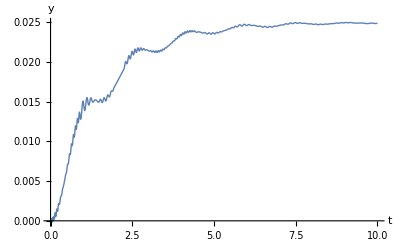

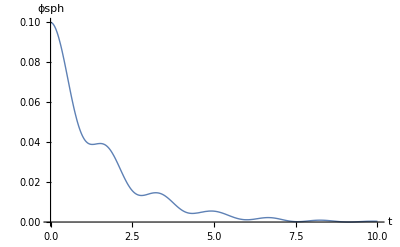

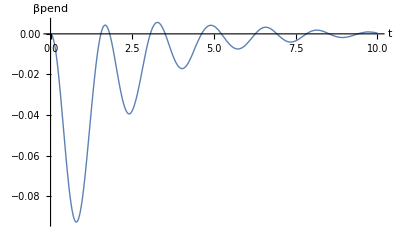

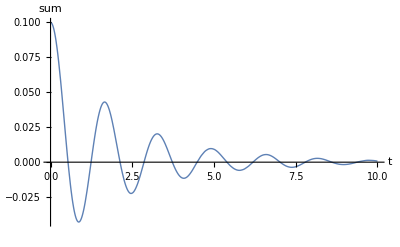

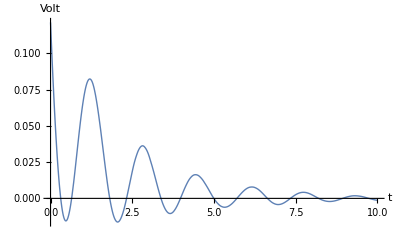

```mathematica
timeEval = 10;

(*coors = Table[ 
{Evaluate[{x[t]}/.s][[1]][[1]],Evaluate[{y[t]}/.s][[1]][[1]]},{t,0,timeEval,0.1}];

ListPlot[coors,PlotRange->All,ImageSize->400, PlotStyle->{Thick, PointSize[Large]},BaseStyle->{20},AxesLabel->{x,y}]*)

(*Plot[Evaluate[{x[t]}/.s],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,x}]*)
Plot[Evaluate[{y[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,y}]

Plot[Evaluate[{ϕsph[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,ϕsph}]
(*Plot[Evaluate[{θsph[t]}/.s],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,θsph}]
Plot[Evaluate[{ψsph[t]}/.s],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,ψsph}]
Plot[Evaluate[{αpend[t]}/.s],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,αpend}]*)
Plot[Evaluate[{βpend[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,βpend}]

Plot[Evaluate[{ϕsph[t]+βpend[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,sum}]

Plot[Evaluate[{Volt[t]}/.solved],{t,0,timeEval},PlotRange->All, ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,Volt}]
```

```mathematica
(*Animate[
params=values;
(*Primer Volante de inercia*)
centroVolante1= Transpose[(VecVol1/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorVolante1 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol1Rot1.{{0},{0},{1}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
inicioVolante1 = (-anchoVolante * 0.5 * directorVolante1 + centroVolante1)/.params;
finVolante1 = (anchoVolante * 0.5 * directorVolante1 + centroVolante1)/.params;
Volante1=Graphics3D[{(*Green,Thick,Arrow[{centroVolante1, centroVolante1 + 10*(finVolante1- centroVolante1)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante1,finVolante1},radioVolante/.params],Axes->True}];
(*Segundo Volante de inercia*)
centroVolante2=
 Transpose[(VecVol2/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorVolante2 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol2Rot1.{{0},{0},{-1}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
inicioVolante2 = (-anchoVolante * 0.5 * directorVolante2 + centroVolante2)/.params;
finVolante2= (anchoVolante * 0.5 * directorVolante2 + centroVolante2)/.params;
Volante2=Graphics3D[{(*Green,Thick,Arrow[{centroVolante2, centroVolante2 + 10*(finVolante2- centroVolante2)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante2,finVolante2},radioVolante/.params],Axes->True}];
(*Péndulo de contrapeso*)
centroPendulo=Transpose[(VecPend/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
Pendulo=Graphics3D[Sphere[centroPendulo,radioVolante]]/.params;
(*Esfera de contenimiento*)
VecCentro=Transpose[(VecEsfera/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{0},{0},{.2}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
LinEsfera=Graphics3D[Arrow[{VecCentro,VecCentro+directorEsfera} ]];
Esfera=Graphics3D[{Opacity[.1],Sphere[VecCentro,radioEsfera/.params]}];

VecContacto=Transpose[(({{x[t]},{y[t]},{0}})/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
Linea=Graphics3D[Line[{{0,0,0},VecContacto}]];

(*Cilidnro del eje de la esfera*)
otroDirectorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{.2},{0},{0}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
LinOtro = Graphics3D[Cylinder[{VecCentro - otroDirectorEsfera,VecCentro+otroDirectorEsfera},0.01 ]];
LinPendulo=Graphics3D[Cylinder[{VecCentro,centroPendulo},0.005 ]];
LinVolantes= Graphics3D[Cylinder[{centroVolante1,centroVolante2},0.005 ]];
Hub=Graphics3D[Sphere[VecCentro,0.02]]/.params;
Arrow1=Graphics3D[{Red,Arrow[{{0,0,0},{0,.21,0}}]}];never a virulent homophobe or anything,I never preached at my gay friends or even explained why I didn't date or go out to gay bars with them;I even supported LGBT civil rights (including marriage) because I thought it was unfair to impose religious beliefs with the force of law.And I defended gay people and their relationships in my religious circles,because I reali
Arrow2=Graphics3D[{Red,Arrow[{{0,0,0},{0,-.08,0}}]}];

Show[{Arrow1,Arrow2,Hub,LinVolantes,Volante1,Volante2,Pendulo,Esfera,LinOtro(*,Linea,LinEsfera,LinOtro*),LinPendulo},PlotRange->{{-.5,.5},{-.5,.5},{0,.5}},ImageSize->900,Axes->{True,True,True},AxesLabel->{x,y,z},Boxed->False],

{varIter,0,10},AnimationRate->1,AnimationRunning->False]*)
```

```mathematica
(*ClearAll["Global`*"]*)
```

```mathematica
(*solveEqs=Eliminate[eq1==0&&eq2==0&&eq3==0&&eq4==0&&eq5==0&&eq6==0&&eq7==0&&eqR1==0&&eqR2==0,{λ1[t],λ2[t]}]*)(*solveEqs=Eliminate[eq2==0&&eq5==0&&eq7==0&&eqR2==0&&D[eqR2,t]==0,{y'[t],y''[t],λ2[t]}];*)
solveEqs=Eliminate[eq2==0&&eq5==0&&eq7==0&&eqR2==0&&D[eqR2,t]==0,{y'[t],y''[t],λ2[t]}];
```

```mathematica
solveSph=Solve[solveEqs,{ϕsph''[t],βpend''[t]}]//Simplify//Chop;
```

```mathematica
ϕpp=ϕsph''[t]/.solveSph[[1]][[1]];
βpp=βpend''[t]/.solveSph[[1]][[2]];
```

```mathematica
(*ϕpp/.values//Expand//Chop;
βpp/.values//Expand//Chop;*)
```

```mathematica
(*Las unicas variables de las que depende el sistema, al menos, directamente, son
βp
ϕp
β+ϕ
y queremos controlar el angulo ϕ
a traves de un controlador que pueda tomar como dato el valor angulo suma β+ϕ
necesitamos por ello alguna forma cerrada que sea como
ϕpp=f(ϕp,βp,ϕ+β)
βpp=f(ϕp,βp,ϕ+β)
(ϕ+β)p=ϕp+βp
y ya, no hay ninguna variable mas en el sistema, pero el angulo ese es una suma, y su derivada se puede calcular de la suma, ok, 
*)
```

```mathematica
(*ϕppϕp=D[ϕpp,ϕsph'[t]]  /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
ϕppϕ  =D[ϕpp,ϕsph[t]]     /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
ϕppβp=D[ϕpp,βpend'[t]]/.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
ϕppβ  =D[ϕpp,βpend[t]]   /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
βppϕp=D[βpp,ϕsph'[t]]  /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
βppϕ  =D[βpp,ϕsph[t]]     /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
βppβp=D[βpp,βpend'[t]]/.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;
βppβ  =D[βpp,βpend[t]]   /.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop;*)
ϕppϕp=D[ϕpp,ϕsph'[t]]/.{Volt[t]->0}   //Chop;
ϕppϕ  =D[ϕpp,ϕsph[t]]/.{Volt[t]->0}      //Chop;
ϕppβp=D[ϕpp,βpend'[t]]/.{Volt[t]->0} //Chop;
ϕppβ  =D[ϕpp,βpend[t]] /.{Volt[t]->0}   //Chop;
βppϕp=D[βpp,ϕsph'[t]]/.{Volt[t]->0}   //Chop;
βppϕ  =D[βpp,ϕsph[t]]/.{Volt[t]->0}      //Chop;
βppβp=D[βpp,βpend'[t]]/.{Volt[t]->0} //Chop;
βppβ  =D[βpp,βpend[t]]/.{Volt[t]->0}    //Chop;
ϕppV  =D[ϕpp,Volt[t]]//Chop;
βppV  =D[βpp,Volt[t]]//Chop;
```

```mathematica
(*ϕppsumA=ϕpp/.{βpend[t]+ϕsph[t]->sum[t]}/.values//Expand
βppsumA=βpp/.{βpend[t]+ϕsph[t]->sum[t]}/.values//Expand*)
```

```mathematica
(*ϕppsum=D[ϕppsumA,sum[t]]/.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop
βppsum=D[βppsumA,sum[t]]/.{sum[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//Chop*)
```

```mathematica
(*SLinA=({{ϕppϕp, ϕppϕ, ϕppβp, ϕppβ}, {1, 0, 0, 0}, {βppϕp, βppϕ, βppβp, βppβ}, {0, 0, 1, 0}})//FullSimplify//Chop;
SLinA//MatrixForm
SLinA/.values//MatrixForm
Det[SLinA]/.values
Eigenvalues[SLinA/.values]//Chop

SLinA=({{ϕppϕp, ϕppβp, ϕppsum}, {βppϕp, βppβp, βppsum}, {1, 1, 0}})//FullSimplify//Chop;
SLinA//MatrixForm
SLinA/.values//MatrixForm
Det[SLinA]/.values
Eigenvalues[SLinA/.values]*)

zerosys={Volt[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0};

SLinA=({{ϕppϕp, ϕppϕ}, {1, 0}}) /.{Volt[t]->0,D[ϕsph[t],t]->fip,ϕsph[t]->fi,D[βpend[t],t]->betap,βpend[t]->beta,Sin->sin,Cos->cos}/.values//Chop;
StringReplace[ExportString[SLinA,"Text"],{"["->"(","]"->")","^"->"**"}];

SLinA=({{ϕppϕp, ϕppϕ}, {1, 0}}) /.{Volt[t]->0,D[ϕsph[t],t]->0,ϕsph[t]->0,D[βpend[t],t]->0,βpend[t]->0}//FullSimplify//Chop;
```

```mathematica
(*ok, entonces necesitamos obtener los autovalores y ajustarlos de manera que *)
A=({{a, b}, {1, 0}});
(*queremos una forma de anadir las ocntribuciones constantes, de manera que quiza ayuden o perjudiquen al voltaje del motor en lugar de que sea siempre constante, esta es porbablemente la amyor contribucion de no linealidad en una region del valor deseado, y este termino incluiria, al menos, la parte no lineal ej mgsintheta, pero podemos ponerla aqui para que el valor del voltaje sea mayor o menor etc*)
B={{cext},{0}};
(*donde la sustitucion para d es*)
drule={cext->c+0*add/Volt[t]};
(*la C se sume unitaria, no hay ninguna D*)

(*en B hace falta la adicion del termino constante que pueda estar como residuo, pero no se como seria una buena manera de ponerlo en las ecuaciones
ademas de eso, la linealizacion, hecha en cualquier punto, supone alguna forma de diferencial sobre los valores de las variables, y entonces en realidad no deseamos estabilizar alrededor de cada punto de la linealizacion, sino dar un valor deseado variable para cada posible linealizacion, quiza multiplicando por algun valor de presescala, y quiza dando el voltaje como un offset para encontrar el termino constante adicional, podria simplemente despreciar esa contribucion, no, no podrias,*)
(*donde*)

K={{k1,k2}};
BK=B.K;
Ap=A-BK;

(*y los eigenvalores son*)
eqc=Det[({{s, 0}, {0, s}})-Ap];
(*con raices*)
Solve[eqc==0,s]
```

{{s→1/2 (a-cext k1-√(a^2+4 b-2 a cext k1+cext^2 k1^2-4 cext k2))},{s→1/2 (a-cext k1+√(a^2+4 b-2 a cext k1+cext^2 k1^2-4 cext k2))}}

```mathematica
(*y donde queremos que la parte real sea muy negativa, y no haya parte imaginaria, por lo que una k1y k2 muy grandes bastarian... pero k2 no...
una posible solucion es hacer que la raiz sea siempre cero a travez de k2, y dejarlo todo en la k1, para que el tiempo de asentamiento en las dos variables sea el mismo, para hacerlo mas facil, quitaremos el posible sobreamortiguamiento del sistema etc...
*)
(*digamos para un asentamiento en dos segundos con un factor de tiempo de 3 veces para asumir termino*)
tto3=2;
invt=1/tto3;
sk1=Solve[(a-cext*k1)/2==-3invt,k1]//Flatten
rec=(-√(a^2+4 b-2 a cext k1+cext^2 k1^2-4 cext k2))/.sk1;
sk2=Solve[rec/2==0,k2]//Flatten
```

{k1→(3+a)/cext}

{k2→(9+4 b)/(4 cext)}

```mathematica
(*Ahora bien, las variables del sistema linealizado son en general diferencias respecto del punto de linealizacion por lo cual, nuestra u que es V debe considerar alguna forma de seguimeinto para contrarestar el valor del punto de evaluacion*)
k0={{0,1}}.Inverse[(-A+BK)].B/.sk1/.sk2
```

{{cext/(-b+1/4 (9+4 b))}}

```mathematica
(*la velocidad entonces no necesita de escalamiento, pero el angulo si, y es el unico valor deseado que tiene sentido porque es la unica salida del sistema, entonces, u esta definida por la relacion*)
k0;
K;
sk1;
sk2;
drule;
values;
u=k0.{{-ϕsph[t]}}-K.{{ϕsph'[t]},{ϕsph[t]}}/.sk1/.sk2/.drule/.{add->ϕpp}/.values;
u1=u[[1]][[1]]//FullSimplify;
u2=u1/.{a->ϕppϕp,b->ϕppV,c->ϕppV}/.values/.{βpend[t]->beta,βpend'[t]->betap,ϕsph[t]->fi,ϕsph'[t]->fip,Cos->cos, Sin->sin};
u3=u2//FullSimplify
(u/.{a->ϕppϕp,b->ϕppV,c->ϕppV}/.values//InputForm)[[1]][[1]][[1]]
```

-1/(90 (-0.419164+0.165691 cos[beta+fi]))(0.427806+0.0323671 cos[fi]-0.0137267 cos[2 (beta+fi)]) (fi (81+(2620.53 (2.52979-1. cos[beta+fi])^2)/(13.2173+1. cos[fi]-0.424096 cos[2 (beta+fi)])^2+(-1165.53+460.72 cos[beta+fi])/(13.2173+1. cos[fi]-0.424096 cos[2 (beta+fi)]))+36 fip (3+(-0.80616+1. fip sin[fi]+(-4.2915 betap-4.2915 fip) sin[beta+fi])/(13.2173+1. cos[fi]-0.424096 cos[2 (beta+fi)])))

-((5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]) ϕsph[t])/(2 (1/4 (9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))-(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])))-((9+(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])) (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph[t])/(10 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))-(2 (0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]) ϕsph'[t] (3+(-0.0260931-0.138903 Sin[βpend[t]+ϕsph[t]] βpend'[t]+0.0323671 Sin[ϕsph[t]] ϕsph'[t]-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])))/(5 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]))

```mathematica
u3text=ExportString[u3,"Text"];
StringReplace[u3text,{"["->"(","]"->")","^"->"**","fi"->"self.fi","beta"->"self.beta"}]
```

-((0.4278062687504448 + 0.032367102026846464*cos(self.fi) - 0.013726746118715057*cos(2*(self.beta + self.fi)))*(self.fi*(81 + (2620.5349931237606*(2.529793316296556 - 1.*cos(self.beta + self.fi))**2)/(13.217317645416836 + 1.*cos(self.fi) - 0.42409561743679086*cos(2*(self.beta + self.fi)))**2 + (-1165.5275189205913 + 460.72045151374016*cos(self.beta + self.fi))/(13.217317645416836 + 1.*cos(self.fi) - 0.42409561743679086*cos(2*(self.beta + self.fi)))) + 36*self.fip*(3 + (-0.8061597714965171 + 1.0000000000000002*self.fip*sin(self.fi) + (-4.2914970338490175*self.betap - 4.2914970338490175*self.fip)*sin(self.beta + self.fi))/(13.217317645416836 + 1.*cos(self.fi) - 0.42409561743679086*cos(2*(self.beta + self.fi))))))/(90*(-0.419163868 + 0.16569095399999997*cos(self.beta + self.fi)))

```mathematica
ϕpp/.values
```

(0.636315 Sin[ϕsph[t]]-0.539717 Sin[2 (βpend[t]+ϕsph[t])]+5/2 (-0.419164+0.165691 Cos[βpend[t]+ϕsph[t]]) Volt[t]-0.0694517 Sin[βpend[t]+ϕsph[t]] βpend'[t]^2-0.0260931 ϕsph'[t]+0.0161836 Sin[ϕsph[t]] ϕsph'[t]^2-0.0694517 Sin[βpend[t]+ϕsph[t]] ϕsph'[t]^2+βpend'[t] ((25 (0.419164-0.165691 Cos[βpend[t]+ϕsph[t]]))/(6 π)-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])

```mathematica
(*necesitamos devolder al sistema original, entonces, lo haremos por pasos y sustituendo ya los valores*)
utmp=u/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values//Expand//InputForm
```

{{(-9*ϕsph[t])/(4*uϕpp) - (0.6363151721109496*Cos[ϕsph[t]]*ϕsph[t])/(uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
      0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + (1.079433903203164*Cos[2*(βpend[t] + ϕsph[t])]*ϕsph[t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) - 
   (0.02059567809694547*Sin[ϕsph[t]]^2*ϕsph[t])/(uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
       0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + (0.034938147276213916*Sin[ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.014817115141203475*Sin[2*(βpend[t] + ϕsph[t])]^2*ϕsph[t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.017993951340281852*Sin[ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + 
   (0.007112814799678484*Cos[βpend[t] + ϕsph[t]]*Sin[ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.21975445295593204*Sin[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + 
   (0.015262311807568804*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][βpend][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.0060330271683663814*Cos[βpend[t] + ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][βpend][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + 
   (0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + 
   (0.002247949003063822*Sin[ϕsph[t]]*Sin[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.0019066906408415402*Sin[βpend[t] + ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][βpend][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - (3*Derivative[1][ϕsph][t])/uϕpp + 
   (0.026093055573967*Derivative[1][ϕsph][t])/(uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
      0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + (0.0008445565919547647*Sin[ϕsph[t]]*ϕsph[t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.0007163454986507356*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + 
   (0.13890332234250014*Sin[βpend[t] + ϕsph[t]]*Derivative[1][βpend][t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + 
   (0.13890332234250014*Cos[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + 
   (0.004495898006127644*Sin[ϕsph[t]]*Sin[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][βpend][t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.0038133812816830803*Sin[βpend[t] + ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][βpend][t]*Derivative[1][ϕsph][t])/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.03236710202684647*Sin[ϕsph[t]]*Derivative[1][ϕsph][t]^2)/(uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
      0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + (0.13890332234250014*Sin[βpend[t] + ϕsph[t]]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) - 
   (0.016183551013423236*Cos[ϕsph[t]]*ϕsph[t]*Derivative[1][ϕsph][t]^2)/(uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
      0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + (0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) - 
   (0.0005238146468081443*Sin[ϕsph[t]]^2*ϕsph[t]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + 
   (0.002247949003063822*Sin[ϕsph[t]]*Sin[βpend[t] + ϕsph[t]]*ϕsph[t]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) + 
   (0.000444294992121069*Sin[ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (0.0019066906408415402*Sin[βpend[t] + ϕsph[t]]*Sin[2*(βpend[t] + ϕsph[t])]*ϕsph[t]*Derivative[1][ϕsph][t]^2)/
    (uϕpp*(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2) - 
   (uϕpp*ϕsph[t])/(-((0.6363151721109496*Cos[ϕsph[t]] - 1.079433903203164*Cos[2*(βpend[t] + ϕsph[t])] - 0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*
         Derivative[1][βpend][t]^2 + 0.016183551013423236*Cos[ϕsph[t]]*Derivative[1][ϕsph][t]^2 - 0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*
         Derivative[1][ϕsph][t]^2 + Derivative[1][βpend][t]*(0.21975445295593204*Sin[βpend[t] + ϕsph[t]] - 0.13890332234250014*Cos[βpend[t] + ϕsph[t]]*
           Derivative[1][ϕsph][t]))/(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])) + 
     ((-0.032367102026846464*Sin[ϕsph[t]] + 0.027453492237430113*Sin[2*(βpend[t] + ϕsph[t])])*(0.6363151721109496*Sin[ϕsph[t]] - 
        0.539716951601582*Sin[2*(βpend[t] + ϕsph[t])] - 0.06945166117125007*Sin[βpend[t] + ϕsph[t]]*Derivative[1][βpend][t]^2 - 
        0.026093055573967*Derivative[1][ϕsph][t] + 0.016183551013423236*Sin[ϕsph[t]]*Derivative[1][ϕsph][t]^2 - 0.06945166117125007*Sin[βpend[t] + ϕsph[t]]*
         Derivative[1][ϕsph][t]^2 + Derivative[1][βpend][t]*((25*(0.419163868 - 0.16569095399999997*Cos[βpend[t] + ϕsph[t]]))/(6*Pi) - 
          0.13890332234250014*Sin[βpend[t] + ϕsph[t]]*Derivative[1][ϕsph][t])))/(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 
        0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2 + 
     (9 + 4*((0.6363151721109496*Cos[ϕsph[t]] - 1.079433903203164*Cos[2*(βpend[t] + ϕsph[t])] - 0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*
            Derivative[1][βpend][t]^2 + 0.016183551013423236*Cos[ϕsph[t]]*Derivative[1][ϕsph][t]^2 - 0.06945166117125007*Cos[βpend[t] + ϕsph[t]]*
            Derivative[1][ϕsph][t]^2 + Derivative[1][βpend][t]*(0.21975445295593204*Sin[βpend[t] + ϕsph[t]] - 0.13890332234250014*Cos[βpend[t] + ϕsph[t]]*
              Derivative[1][ϕsph][t]))/(0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])]) - 
         ((-0.032367102026846464*Sin[ϕsph[t]] + 0.027453492237430113*Sin[2*(βpend[t] + ϕsph[t])])*(0.6363151721109496*Sin[ϕsph[t]] - 
            0.539716951601582*Sin[2*(βpend[t] + ϕsph[t])] - 0.06945166117125007*Sin[βpend[t] + ϕsph[t]]*Derivative[1][βpend][t]^2 - 
            0.026093055573967*Derivative[1][ϕsph][t] + 0.016183551013423236*Sin[ϕsph[t]]*Derivative[1][ϕsph][t]^2 - 
            0.06945166117125007*Sin[βpend[t] + ϕsph[t]]*Derivative[1][ϕsph][t]^2 + Derivative[1][βpend][t]*
             ((25*(0.419163868 - 0.16569095399999997*Cos[βpend[t] + ϕsph[t]]))/(6*Pi) - 0.13890332234250014*Sin[βpend[t] + ϕsph[t]]*Derivative[1][ϕsph][t])))/
          (0.4278062687504448 + 0.032367102026846464*Cos[ϕsph[t]] - 0.013726746118715057*Cos[2*(βpend[t] + ϕsph[t])])^2))/4)}}

```mathematica
(*ahora, u, o la ley de control, es simplemente*)
ulc=-k1*ϕsph'[t]-k2*ϕsph[t]/.sk1/.sk2
ulcnumeval=(-k1/.sk1/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values/.zerosys)*ϕsph'[t]+(-k2/.sk2/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values/.zerosys)*ϕsph[t]/.sk1/.sk2
(*pero quiero una expresion simbolica para el solver, y para poner en el programa tambien etc*)
ulcnumsymb=(-k1/.sk1/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values)*ϕsph'[t]+(-k2/.sk2/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values)*ϕsph[t]/.sk1/.sk2//Expand;
k1sym=(-k1/.sk1/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values)
k2sym=(-k2/.sk2/.{a->ϕppϕp,b->ϕppϕ,c->uϕpp}/.values)
```

-((9+4 b) ϕsph[t])/(4 cext)-((3+a) ϕsph'[t])/cext

-(1.25745 ϕsph[t])/cext-(2.94155 ϕsph'[t])/cext

-(3+(-0.0260931-0.138903 Sin[βpend[t]+ϕsph[t]] βpend'[t]+0.0323671 Sin[ϕsph[t]] ϕsph'[t]-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])]))/cext

-1/(4 cext)(9+4 ((0.636315 Cos[ϕsph[t]]-1.07943 Cos[2 (βpend[t]+ϕsph[t])]-0.0694517 Cos[βpend[t]+ϕsph[t]] βpend'[t]^2+0.0161836 Cos[ϕsph[t]] ϕsph'[t]^2-0.0694517 Cos[βpend[t]+ϕsph[t]] ϕsph'[t]^2+βpend'[t] (0.219754 Sin[βpend[t]+ϕsph[t]]-0.138903 Cos[βpend[t]+ϕsph[t]] ϕsph'[t]))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])-((-0.0323671 Sin[ϕsph[t]]+0.0274535 Sin[2 (βpend[t]+ϕsph[t])]) (0.636315 Sin[ϕsph[t]]-0.539717 Sin[2 (βpend[t]+ϕsph[t])]-0.0694517 Sin[βpend[t]+ϕsph[t]] βpend'[t]^2-0.0260931 ϕsph'[t]+0.0161836 Sin[ϕsph[t]] ϕsph'[t]^2-0.0694517 Sin[βpend[t]+ϕsph[t]] ϕsph'[t]^2+βpend'[t] ((25 (0.419164-0.165691 Cos[βpend[t]+ϕsph[t]]))/(6 π)-0.138903 Sin[βpend[t]+ϕsph[t]] ϕsph'[t])))/(0.427806+0.0323671 Cos[ϕsph[t]]-0.0137267 Cos[2 (βpend[t]+ϕsph[t])])^2))

```mathematica
ulcnumsymb//InputForm;
k1sym//InputForm;
```

```mathematica
SLinA//MatrixForm
SLinA/.values//MatrixForm
Det[SLinA]/.values
Eigenvalues[SLinA/.values]
SLinB={{uϕpp},{uβpp},{0}}//FullSimplify//Chop;
SLinB//MatrixForm//Chop
SLinB={{uϕpp},{0}}//FullSimplify//Chop;
SLinB/.values//MatrixForm//Chop
```

((fEsfYAir radioEsfera^2 (-1. IxxP-1. mPend radioPendulo^2))/(IxxP (1. IxxS+1. mEsf offsetEsf^2+2. mEsf offsetEsf radioEsfera+1. mEsf radioEsfera^2+1. mPend radioEsfera^2)+mPend (1. IxxS+mEsf (1. offsetEsf^2+2. offsetEsf radioEsfera+1. radioEsfera^2)) radioPendulo^2) | (g (1. IxxP mEsf offsetEsf+mPend (1. mEsf offsetEsf-1. mPend radioEsfera) radioPendulo^2))/(IxxP (1. IxxS+1. mEsf offsetEsf^2+2. mEsf offsetEsf radioEsfera+1. mEsf radioEsfera^2+1. mPend radioEsfera^2)+mPend (1. IxxS+1. mEsf offsetEsf^2+2. mEsf offsetEsf radioEsfera+1. mEsf radioEsfera^2) radioPendulo^2)
1 | 0)

(-0.0584461 | -0.992546
1 | 0)

0.992546

{-0.029223+0.995837 ⅈ,-0.029223-0.995837 ⅈ}

(uϕpp
uβpp
0)

(uϕpp
0)

```mathematica
(*Intentaremos primero hacer el controlador para el sistema de orden minimo, con solamente una mtriz de dos por dos y ya*)
SSM=StateSpaceModel[{SLinA/.values,SLinB/.values,{{0,1}}}]
```

-0.0584461-0.992546uϕpp100010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
(*Este sistema es para el caso en que se tienen solamente dos estados, referentes al angulo de la placa del pendulo y nada mas, y la entrada es el voltaje al sistema, por supuesto, es un sistema lineal etc. etc. y no es lo mismo, pero el comportamiento de estabilidad parace estar correctamente, en todos los posibles casos, para dos a cuatro posibles variables de estado*)
Clear[s]
TFM=TransferFunctionModel[SSM,s]
```

uϕpp/(0.992546+0.0584461 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`u0.99254581985269361FalseFalseFalseAutomaticNoneAutomatic

```mathematica
pid=PIDTune[TFM,{"P","ZieglerNichols"},"PIDData"]
```

PIDTune::idm: Unable to determine the static gain, time constant and time delay using the parameter estimator Automatic. Try a different method.

PIDTune[uϕpp/(0.992546+0.0584461 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`u0.99254581985269361FalseFalseFalseAutomaticNoneAutomatic,{P,ZieglerNichols},PIDData]

```mathematica
pid["FeedbackIdealParameters"]
```

PIDTune[uϕpp/(0.992546+0.0584461 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`u0.99254581985269361FalseFalseFalseAutomaticNoneAutomatic,{P,ZieglerNichols},PIDData][FeedbackIdealParameters]